```mathematica
Directory[]
Print["Hallo Welet"]
target=Rest@$ScriptCommandLine;
splitTarget=StringSplit[target,"|"];
{inputstringF,inputstringFilePath,inputstringParams,inputstringStartVal,inputstringRanges,inputstringSteps,inputstringfixedParams,inputstringfixedValues,inputstringanglestep,inputstringIterations}=Flatten@Table[s,{s,splitTarget}];
```

C:\Users\Jonas\Documents

Hallo Welet

Rest::norest: Cannot take Rest of expression {} with length zero.

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[Rest[{}],|].

Table::iterb: Iterator {s,StringSplit[Rest[{}],|]} does not have appropriate bounds.

Set::shape: Lists {inputstringF,inputstringFilePath,inputstringParams,inputstringStartVal,inputstringRanges,inputstringSteps,inputstringfixedParams,inputstringfixedValues,inputstringanglestep,inputstringIterations} and Table[s,{s,StringSplit[Rest[{}],|]}] are not the same shape.

```mathematica
(*F[B_,θB_,ϕB_,M_,θ_,ϕ_]=M*B(Sin[θ]*Sin[θB]*Cos[ϕ-ϕB]+Cos[θ]*Cos[θB])-(1/2*μ0*M^2-K2s)Sin[θ]^2-K2p*Sin[θ]^2*Cos[ϕ-ϕu]^2-1/2*K4s*Cos[θ]^4-1/8*K4p(3+Cos[4*ϕ])Sin[θ]^4;*)
ToExpression[inputstringF];
Print[inputstringF]
hl=Simplify[1/(M^2 Sin[θ]^2)(D[F[B,θB,ϕB,M,θ,ϕ],{θ,2}]D[F[B,θB,ϕB,M,θ,ϕ],{ϕ,2}]-(D[F[B,θB,ϕB,M,θ,ϕ],θ,ϕ])^2)];
ResField[θB_,ϕB_,M_,θ_,ϕ_]=(B/.Solve[hl==(ω/γ)^2,B])[[2]];(*Not sure if Number 2 is automatically the physically valid solution*)

SolveAngles[B_,θB_,ϕB_,rule_]:=(Sort[Table[Quiet@FindMinimum[{F[B,θB,ϕB,M,θ,ϕ]/.rule},{{ϕ,ϕB-n π/8.},{θ,θB-m π/8.}}],{n,-1,1},{m,-1,1}],#1[[1]]<#2[[1]]&][[1,2]])
angleFunc[B_,θB_,ϕB_,rule_]:={θ,ϕ}/.(SolveAngles[B,θB,ϕB,rule][[2]]);

ResFieldNumInp[θB_,ϕB_,rule_]:=(ResField[θB,ϕB,M,#[[1]],#[[2]]]/.rule)&[angleFunc[BinterAligned[ϕB],θB,ϕB,rule]];
```

14.180854

C:\Users\Jonas\Desktop\Mathematica to Python

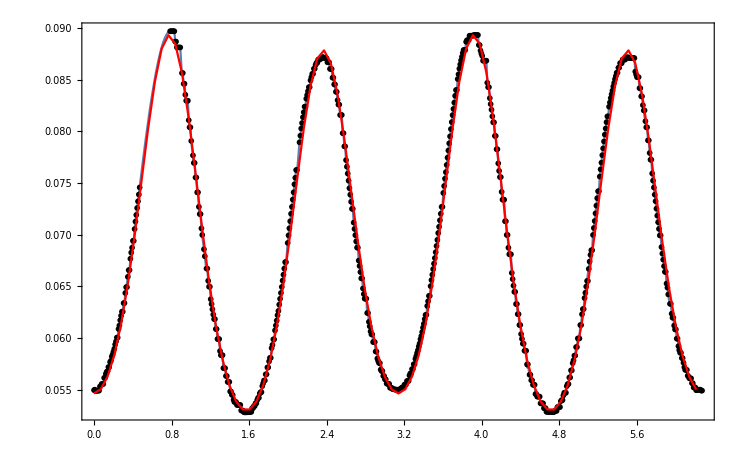

```mathematica
para = Import[inputStringFilePath,"Table"];
data=Transpose[{Table[para[[i,7]],{i,1,Length[#]}],#}&@Map[#[[3]]&,para]][[18;;-20]];

(*data=Sort[Transpose[{Mod[Transpose[data][[1,1;;Length[Transpose[data][[1]]]-1]]-20,180],
Transpose[data][[2,1;;Length[Transpose[data][[2]]]-1]]}]];*)(*Readjust the position of the Anisotropy peaks (might be complicated, depending on how the data looks like)*)
Shift=37;
interTab=Sort@DeleteDuplicates@Transpose[{π/180 Mod[#[[1]],360],#[[2]]}&@(Transpose[data]+{Shift,0})];
ϕmin=Min[Transpose[interTab][[1]]];
ϕmax=Max[Transpose[interTab][[1]]];
BinterAligned=Check[Interpolation[interTab],0];
fitParameters=ToExpression[inputStringParams](*{K2p,K2s,K4p,ϕu}*);

(*startvalues={startk2p,startk2s,startk4p,startk4s};*)
startvalues=ToExpression[inputstringStartVal](*{863.25,261345,13720.6,5.07568359375}*);
ranges=ToExpression[inputstringRanges](*{0.5,0.5,0.5,0.5}*);(*The ranges as a fraction of the starting Parameters eg.: 0.5 -> Try fitting from startvalue - 0.5*starvalue to startvalue + 0.5*startvalue*)
steps=ToExpression[inputstringSteps](*{0.5,0.5,0.5,0.5}*);(*The steps to take while fitting, as a fraction of the ranges*)

fixedParameters=ToExpression[inputstringfixedParams](*{ω,g,M,K4s}*);
fixedParameterValues=ToExpression[inputstringfixedValues](*{2π*9.8782*10^9,2.05,1.53*10^6,0}*);

constants={μ0,μb,ℏ};
constantValues={4*π*10^-7,9.27*10^-24,(6.62606957*10^-34)/(2π)};

angleStep=ToExpression[inputstringanglestep](*π/45*);

γ=(g*μb)/ℏ;
parameterRules=Table[fixedParameters[[i]]->fixedParameterValues[[i]],{i,1,Length[fixedParameters]}];
constantRules=Table[constants[[i]]->constantValues[[i]],{i,1,Length[constants]}];
rules=Flatten[{parameterRules,constantRules}];

pre=Table[{ϕB,ResFieldNumInp[π/2,ϕB,Flatten[{Table[fitParameters[[l]]->startvalues[[l]],{l,1,Length[startvalues]}],rules}]]},{ϕB,ϕmin,ϕmax,angleStep}];

Show[Plot[BinterAligned[ϕ],{ϕ,ϕmin,ϕmax},GridLines->{Table[i,{i,-2π,2π,π/32}],Automatic},Frame->True,PlotRange->All],ListPlot[interTab,PlotStyle->Black],ListLinePlot[pre,PlotStyle->Red,PlotRange->All]]
```

{K2p→863.251,K2s→261345.,K4p→13720.6,ϕu→5.07568}

835.103

Evaluation Time: 263.5145663

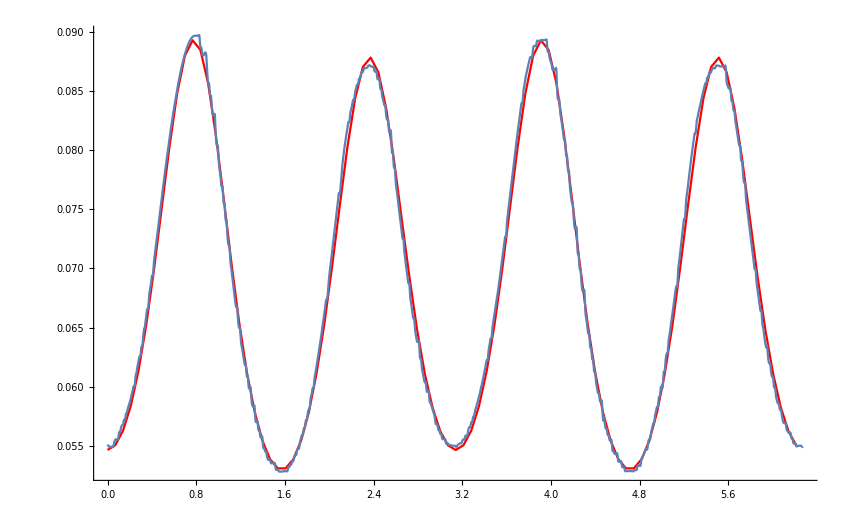

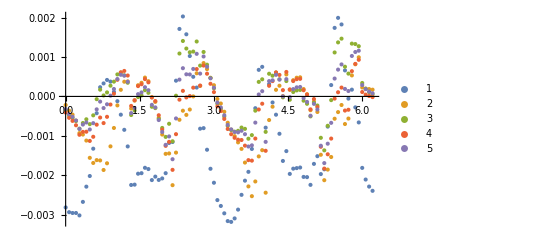

```mathematica
iterations=ToExpression[inputstringIterations](*5*);
fitParamsEvolution={};
run=True;
If[Length[constants]≠Length[constantValues],Print["ConstatsTables are of unequal Length. Skipping Evaluation"];run=False]
If[Length[fixedParameters]≠Length[fixedParameterValues],Print["ParameterTables are of unequal Length. Skipping Evaluation"];run=False]
If[Length[fitParameters]≠Length[ranges],Print["Ranges are of unequal Length. Skipping Evaluation"];run=False]
If[Length[fitParameters]≠Length[steps],Print["Steps are of unequal Length. Skipping Evaluation"];run=False]
If[Length[fitParameters]≠Length[startvalues],Print["Startvalues are of unequal Length. Skipping Evaluation"];run=False]
If[run,
For[i=1,i≤iterations,i++,
iterationInstructions=Tuples[Table[Table[fitParameters[[ii]]->l,{l,startvalues[[ii]](1-ranges[[ii]]),startvalues[[ii]](1+ranges[[ii]]),startvalues[[ii]]*ranges[[ii]]*steps[[ii]]}],{ii,1,Length[fitParameters]}]];
difftab=ParallelTable[Sum[Abs[ResFieldNumInp[π/2,ϕB,Flatten[{it,rules}]]-BinterAligned[ϕB]],{ϕB,ϕmin,ϕmax,angleStep}],{it,iterationInstructions}];
pos=Position[difftab,Min[difftab]][[1,1]];
AppendTo[fitParamsEvolution,iterationInstructions[[pos]]];
startvalues=fitParameters/.iterationInstructions[[pos]];
ranges=0.5*ranges;(*The ranges as a fraction of the starting Parameters eg.: 0.5 -> Try fitting from startvalue - 0.5*starvalue to startvalue + 0.5*startvalue*)
];
fittedParams=iterationInstructions[[pos]]
]
Min[difftab]/Length[Table[1,{ϕB,ϕmin,ϕmax,angleStep}]]*(M/.rules)
tmp=ParallelTable[{ϕB,ResFieldNumInp[π/2,ϕB,Flatten[{fittedParams,rules}]]},{ϕB,ϕmin,ϕmax,angleStep}];
Show[ListLinePlot[tmp,PlotStyle->Red],Plot[BinterAligned[ϕB],{ϕB,ϕmin,ϕmax}],PlotRange->All]
tmp2=Table[ParallelTable[{ϕB,ResFieldNumInp[π/2,ϕB,Flatten[{i,rules}]]-BinterAligned[ϕB]},{ϕB,ϕmin,ϕmax,angleStep}],{i,fitParamsEvolution}];
ListPlot[tmp2,PlotLegends->Table[i,{i,1,Length[fitParamsEvolution]}],PlotRange->All]
```

{863.251,261345.,13720.6,0,5.07568}

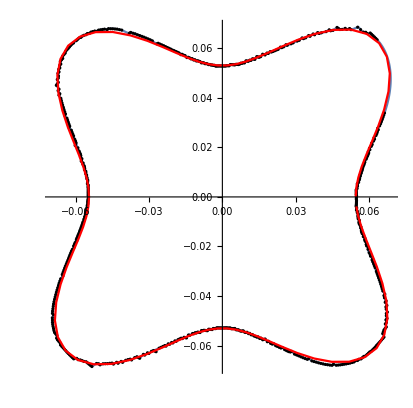

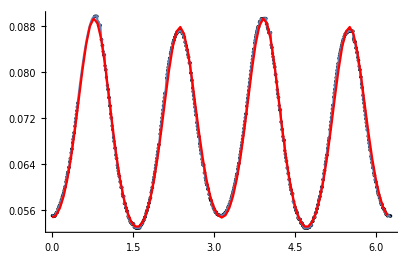

```mathematica
Konstanten = {K2p /. fittedParams,K2s /. fittedParams,K4p /. fittedParams,0,ϕu /.fittedParams}
polarplot = Show[PolarPlot[BinterAligned[ϕB],{ϕB,ϕmin,ϕmax}],ListPolarPlot[BinterAligned,PlotRange->All,PlotStyle->Black],ListPolarPlot[tmp,Joined->True,PlotStyle->Red]]
plot = Show[ListPlot[BinterAligned,PlotStyle->Black],Plot[BinterAligned[ϕB],{ϕB,ϕmin,ϕmax}],ListLinePlot[tmp,PlotStyle->Red],PlotRange->All]
Export["PolarPlot-FeRh-3-IP-NEW-MS.pdf",polarplot];
Export["Plot-FeRh-3-IP-NEW-MS.pdf",plot];
Export["Anisotropie-Konstanten-FeRh-3-IP-NEW-MS.dat",Konstanten];
Export["Funktion-FeRh-3-IP-NEW-MS.dat",tmp];
```

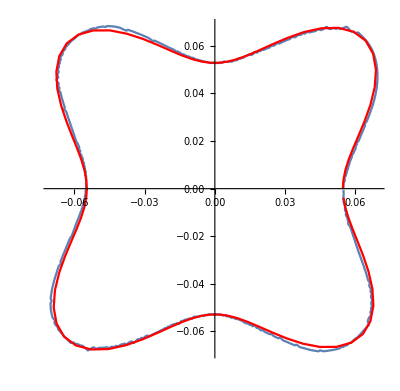

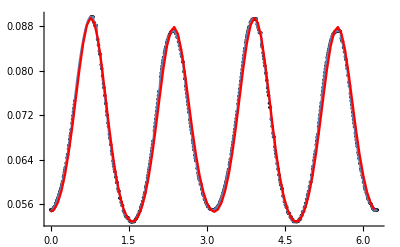

```mathematica
polarplot = Show[PolarPlot[BinterAligned[ϕB],{ϕB,ϕmin,ϕmax}],ListPolarPlot[tmp,Joined->True,PlotStyle->Red]]
plot = Show[ListPlot[BinterAligned,PlotStyle->Black],Plot[BinterAligned[ϕB],{ϕB,ϕmin,ϕmax}],ListLinePlot[tmp,PlotStyle->Red],PlotRange->All]
```